```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3, 0≤x≤1/2}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3, 1/2<x≤3/2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Continuity*)
C1l=Simplify[h[x],0≤x≤1/2]/.x->1/2
C1r=Simplify[h[x],1/2<x≤3/2]/.x->1/2
C2l=Simplify[h[x],1/2<x≤3/2]/.x->3/2
C2r=Simplify[h[x],3/2<x≤5/2]/.x->3/2
C3l=Simplify[h[x],3/2<x≤5/2]/.x->5/2
```

1+c01/2+c02/4+c03/8

1/2 (-c11+1/2 (c12-c13/2))

1/2 (c11+1/2 (c12+c13/2))

1/2 (-c21+1/2 (c22-c23/2))

1/2 (c21+1/2 (c22+c23/2))

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c01,c02+2 (c12+c22),c03}

{0,-2 c11-4 c21,0,-2 (c13+2 c23)}

```mathematica
GenSols=Solve[{
	C1l==C1r,
	C2l==C2r,
	C3l==0,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T1[[2]]==1,
	T1[[4]]==0
	},
	{c01,c02,c03,c11,c12,c13,c21,c22,c23}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c01→0,c03→0,c12→1,c13→-6-2 c02-4 c11,c21→-1/4-c11/2,c22→-1-c02/2,c23→3+c02+2 c11}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
SumF1=SumF1/.φ->1/2;
```

```mathematica
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>3-1/2&&y<4-1/2]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-3-1/2&&y<-2-1/2]
}];
```

```mathematica
TableForm[{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}]
TableForm[{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}]
```

1/64 (-8 (-1+(2-3 c11) y+(1+3 c02) y^2+6 (3+c02+2 c11) y^3)-2 x^2 (1+2 y) (4-(1+14 c11) y+18 c02^2 y^2+14 (3+2 c11) y^2+2 c02 (6-(10+9 c11) y+2 (17+9 c11) y^2))+x (16-3 y+2 (7+4 c02) y^2+8 (3+c02) y^3+52 c11^2 y (-1+4 y^2)+4 c11 (-6-2 y-(7+9 c02) y^2+(82+26 c02) y^3))-8 x^3 (c02^2 y^2 (-9+26 y)+26 c11^2 y (-1+4 y^2)+3 (-6-y-7 y^2+78 y^3)+c11 (-12-41 y-14 y^2+312 y^3)+c02 (-6-(1+13 c11) y-2 (17+9 c11) y^2+52 (3+2 c11) y^3)))
1/32 (-77+28 x-47 x^2+234 x^3+221 y-58 x y+59 x^2 y-858 x^3 y-204 y^2+55 x y^2-48 x^2 y^2+852 x^3 y^2+60 y^3-18 x y^3+12 x^2 y^3-288 x^3 y^3-4 c02^2 x^2 (-1+y)^2 (13+8 (-1+x) y)-8 c11^2 x (-1+4 x^2) (-3+11 y-12 y^2+4 y^3)-2 c11 (15-55 y+60 y^2-20 y^3+x (15-55 y+53 y^2-18 y^3)+x^2 (3-11 y+12 y^2-4 y^3)+2 x^3 (-75+275 y-286 y^2+96 y^3))+c02 (2 (-1+y)^2 (-17+10 y)+x (-1+y)^2 (9+2 (-3+8 c11) y)+x^2 (-163+401 y-352 y^2+100 y^3+16 c11 (-3+11 y-12 y^2+4 y^3))-2 x^3 (-39+191 y-238 y^2+96 y^3+8 c11 (-3+15 y-20 y^2+8 y^3))))
1/32 (-(1+x) (3+2 x) (5+6 x+2 c02 (1+x)+c11 (2+4 x)) (1+c02 (-1+y)^2)+4 (-1-x) (-1+c11-x-2 (3+c02+2 c11) (1+x)^2) (-1+y) (-1+c11-2 (3+c02+2 c11) (-1+y)^2+y)-7 (1+x) (3+2 x) (5+6 x+2 c02 (1+x)+c11 (2+4 x)) (-1+y) (-1+c11-2 (3+c02+2 c11) (-1+y)^2+y)+(1+c02 (1+x)^2) (-1+y) (-3+2 y) (-5+2 c02 (-1+y)+6 y+c11 (-2+4 y))+7 (-1-x) (-1+c11-x-2 (3+c02+2 c11) (1+x)^2) (-1+y) (-3+2 y) (-5+2 c02 (-1+y)+6 y+c11 (-2+4 y))-2 (1+x) (3+2 x) (5+6 x+2 c02 (1+x)+c11 (2+4 x)) (-1+y) (-3+2 y) (-5+2 c02 (-1+y)+6 y+c11 (-2+4 y)))
1/128 (-2+y) (-4 (1+x) (3+2 x) (5+6 x+2 c02 (1+x)+c11 (2+4 x)) (-2+c11-2 (3+c02+2 c11) (-2+y)^2+y)+4 (-1-x) (-1+c11-x-2 (3+c02+2 c11) (1+x)^2) (-5+2 y) (-11+2 c02 (-2+y)+6 y+c11 (-6+4 y))-7 (1+x) (3+2 x) (5+6 x+2 c02 (1+x)+c11 (2+4 x)) (-5+2 y) (-11+2 c02 (-2+y)+6 y+c11 (-6+4 y)))
-1/128 (2+x) (5+2 x) (11+6 x+2 c02 (2+x)+c11 (6+4 x)) (-2+y) (-5+2 y) (-11+2 c02 (-2+y)+6 y+c11 (-6+4 y))
0

1/64 (-96+432 x-424 x^2+144 x^3-9 y-41 x y+58 x^2 y-24 x^3 y-94 y^2+358 x y^2-424 x^2 y^2+168 x^3 y^2-2160 y^3+5928 x y^3-5784 x^2 y^3+1872 x^3 y^3+52 c11^2 (-3+11 x-12 x^2+4 x^3) y (-1+4 y^2)+4 c02^2 (-1+x)^2 y^2 (-9-70 y+2 x (9+26 y))+4 c11 (-3 (6-31 y+7 y^2+198 y^3)+x^3 (24-82 y+28 y^2+624 y^3)+x (66-258 y+77 y^2+1846 y^3)-x^2 (72-253 y+84 y^2+1900 y^3))+4 c02 (c11 y (35-27 y-218 y^2)-2 (3+25 y^2+195 y^3)+2 x^3 (6-(1+13 c11) y+2 (17+9 c11) y^2+52 (3+2 c11) y^3)+x (24-2 (1+48 c11) y+(178+99 c11) y^2+10 (107+67 c11) y^3)-x^2 (30-(4+87 c11) y+2 (95+54 c11) y^2+4 (251+165 c11) y^3)))
1/32 (-106+636 x-655 x^2+234 x^3-636 y+2514 x y-2515 x^2 y+858 x^3 y-655 y^2+2515 x y^2-2508 x^2 y^2+852 x^3 y^2-234 y^3+858 x y^3-852 x^2 y^3+288 x^3 y^3+4 c02^2 (-1+x)^2 (1+y)^2 (13+8 x y)+8 c11^2 (-3+11 x-12 x^2+4 x^3) (3+11 y+12 y^2+4 y^3)+2 c11 (-3 (39+143 y+149 y^2+50 y^3)+11 x (39+143 y+149 y^2+50 y^3)+2 x^3 (75+275 y+286 y^2+96 y^3)-x^2 (447+1639 y+1704 y^2+572 y^3))+c02 (110+(83-48 c11) y-(71+96 c11) y^2-6 (13+8 c11) y^3+2 x^3 (39+191 y+238 y^2+96 y^3+8 c11 (3+15 y+20 y^2+8 y^3))-x^2 (71+745 y+1076 y^2+476 y^3+32 c11 (3+17 y+24 y^2+10 y^3))+x (-83+368 y+745 y^2+382 y^3+16 c11 (3+22 y+34 y^2+15 y^3))))
1/32 (6251-9032 x+4369 x^2-702 x^3+17475 y-25382 x y+12281 x^2 y-1974 x^3 y+16478 y^2-23931 x y^2+11576 x^2 y^2-1860 x^3 y^2+5112 y^3-7422 x y^3+3588 x^2 y^3-576 x^3 y^3-16 c11^2 (-30+47 x-24 x^2+4 x^3) (3+11 y+12 y^2+4 y^3)-4 c02^2 (-2+x)^2 (1+y)^2 (-43-36 y+4 x (5+4 y))-2 c11 (2 x^3 (189+593 y+598 y^2+192 y^3)-3 (1011+3207 y+3254 y^2+1048 y^3)-x^2 (2301+7237 y+7308 y^2+2348 y^3)+x (4605+14535 y+14707 y^2+4730 y^3))+c02 (-2 x^3 (237+665 y+622 y^2+192 y^3)+4 (1049+2945 y+2764 y^2+858 y^3)+x^2 (2945+8267 y+7744 y^2+2396 y^3)-x (6089+17096 y+16033 y^2+4970 y^3)-8 c11 (-2+x) (1+y) (4 x^2 (8+17 y+8 y^2)+3 (43+93 y+44 y^2)-x (131+280 y+132 y^2))))
1/128 (-38812+55918 x-26432 x^2+4104 x^3-55918 y+80295 x y-37952 x^2 y+5892 x^3 y-26432 y^2+37952 x y^2-17936 x^2 y^2+2784 x^3 y^2-4104 y^3+5892 x y^3-2784 x^2 y^3+432 x^3 y^3+12 c11^2 (-30+47 x-24 x^2+4 x^3) (30+47 y+24 y^2+4 y^3)+4 c02^2 (-2+x)^2 (2+y)^2 (-95-34 y+2 x (17+6 y))+4 c11 (-2+x) (2+y) (4 x^2 (153+152 y+36 y^2)-8 x (321+320 y+76 y^2)+3 (855+856 y+204 y^2))+2 c02 (-2+x) (2+y) (3860+3457 y+750 y^2+2 x^2 (375+334 y+72 y^2)-x (3457+3088 y+668 y^2)+2 c11 (1020+979 y+226 y^2+x^2 (226+212 y+48 y^2)-x (979+928 y+212 y^2))))
1/128 (-39142+38170 x-12320 x^2+1320 x^3-56763 y+55173 x y-17808 x^2 y+1908 x^3 y-27132 y^2+26372 x y^2-8512 x^2 y^2+912 x^3 y^2-4284 y^3+4164 x y^3-1344 x^2 y^3+144 x^3 y^3+4 c02^2 (-3+x)^2 (-7+2 x) (2+y)^2 (5+2 y)+4 c11^2 (-105+107 x-36 x^2+4 x^3) (30+47 y+24 y^2+4 y^3)+4 c11 (21-13 x+2 x^2) (10+9 y+2 y^2) (-53-32 y+4 x (5+3 y))+2 c02 (21-13 x+2 x^2) (10+9 y+2 y^2) (-67-35 y+x (23+12 y)+2 c11 (-19-11 y+x (7+4 y))))
1

```mathematica
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5}=Parallelize[{
	Simplify[D[SumF1a1,{{x,y}}]],
	Simplify[D[SumF1a2,{{x,y}}]],
	Simplify[D[SumF1a3,{{x,y}}]],
Simplify[D[SumF1a4,{{x,y}}]],
Simplify[D[SumF1a5,{{x,y}}]],
	Simplify[D[SumF1b1,{{x,y}}]],
	Simplify[D[SumF1b2,{{x,y}}]],
	Simplify[D[SumF1b3,{{x,y}}]],
Simplify[D[SumF1b4,{{x,y}}]],
Simplify[D[SumF1b5,{{x,y}}]]
}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1b1,Err1b2,Err1b3,Err1b4,Err1b5}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-2-1/2)^(-1-1/2) (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(3-1/2)^(4-1/2) (DSumF1b5.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5];
```

```mathematica
Err=Err1
DErr=FullSimplify[D[Err,{{c02,c11}}]];
H=FullSimplify[D[Err,{{c02,c11},2}]];
Sols=Solve[DErr==0,{c02,c11}];
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1/12902400(638955 c02^4+c02^3 (7449812-12024 c11)+12 c02^2 (3036379+6 c11 (1765+2348 c11))+96 c02 (786959+c11 (109083+4 c11 (10004+503 c11)))+96 (633789+2 c11 (155618+c11 (70367+4194 c11+4024 c11^2))))

1 | 0.0902019 | True
2 | 1.51531+0.202274 ⅈ | False
3 | 1.51531-0.202274 ⅈ | False
4 | 1.62536+2.08458 ⅈ | False
5 | 1.62536-2.08458 ⅈ | False
6 | -0.624601+3.89872 ⅈ | False
7 | -0.624601-3.89872 ⅈ | False
8 | -0.218441+3.24005 ⅈ | False
9 | -0.218441-3.24005 ⅈ | False

```mathematica
RootReduce[Sols[[1]]]
```

{c02→Root[95847501175547613564801600+290787026673489172616069184 #1+427693530277085972126756216 #1^2+374454369419578668527648440 #1^3+206526493409660806096287626 #1^4+73985811686932641040952616 #1^5+17333088289108701496879625 #1^6+2585430622222421745766995 #1^7+224999970811293497663025 #1^8+8794043350198430409225 #1^9&,1],c11→Root[186034729797937411538022907705+266195094834401033071061383245 #1+23814746789073430925129080750 #1^2-74579241765856896300539908358 #1^3-31992383923550463074170477624 #1^4+27118665196708626294219280904 #1^5+12658942797006126318184281760 #1^6+12703022498519592874591024320 #1^7+1336110826973695570314316800 #1^8+1509855165491135315913446400 #1^9&,1]}

{c01→0.,c03→0.,c12→1.,c13→0.463315,c21→0.162576,c22→-0.209324,c23→-0.231657,c02→-1.58135,c11→-0.825153}

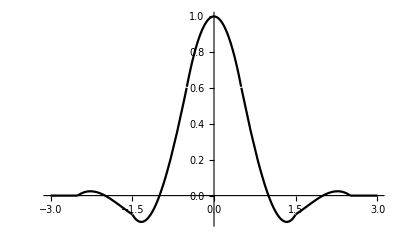

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```